tamoaltas - Graficas de serie de Fourier.
-Graphics-

```mathematica
(* Constantes *)
A = 3;
L = 1;
```

```mathematica
(* Se define la onda cuadrada *)
ondaCuadrada[x_]:=Piecewise[{{A,-L/2<x<L/2},{0,Abs[x] >= L/2}}]
```

```mathematica
(* Aproximación de serie de Fourier *)
serieFourier[x_,n_]:=(A L)/(2 Pi)+(2A)/Pi Sum[  (Sin[k L/2] Cos[k x])/k,{k,1,n}]
```

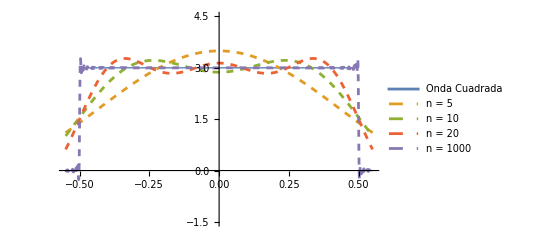

```mathematica
(* Se grafican las ondas *)
xp = L/2*0.1; yp = A*0.5;
plot = Plot[{ondaCuadrada[x],serieFourier[x,5],serieFourier[x,10],serieFourier[x,20],serieFourier[x,1000]},
{x,-(L/2+xp),L/2+xp},
PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed},
PlotLegends->{"Onda Cuadrada", "n = 5", "n = 10", "n = 20", "n = 1000"},
PlotRange->{{-(L/2+xp),L/2+xp},{-yp,A+yp}}]
```

Conforme “n” aumenta,  el centro del rectángulo se aplana más y más, mientras los extremos empiezan a osicilar más, y a mayor amplitud. En los puntos de discontunidad, la pendiente de la curva se va haciendo vertical.

```mathematica
imagesDir=FileNameJoin[{NotebookDirectory[],"/images" }];
plotName= StringJoin[ {FileBaseName[NotebookFileName[]], ".png"}];
filePath= FileNameJoin[{imagesDir,plotName}];

(* Se crea el directorio si no existe *)
If[!DirectoryQ[imagesDir],CreateDirectory[imagesDir]];

Rasterize[plot,ImageResolution->Automatic,Background->White];
```

```mathematica
Export[filePath,plot,ImageResolution->Automatic];
```